# BB8: SVD

## Eric Miller - QEA - April 13, 2016

## Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

Eventually, these functions may want to use the Notation` package to actually make the subscripted letters have downvalues. For now, I’m just being careful.

```mathematica
Clear@ClearSubscripts
ClearSubscripts[top_]:=(
(Unset[Evaluate[#[[1]]]];Evaluate[#[[1]]])&/@Select[DownValues[Subscript],#[[1,1,1]]==top&]
)
Clear@unknownArray
unknownArray[top_,dim_/;NumberQ[dim]]:=(
Table[Subscript[top, i],{i,dim}]
)
unknownArray[top_,{dim1_/;NumberQ[dim1],dim2_/;NumberQ[dim2]}]:=(
Table[Subscript[top, i,j],{i,dim1},{j,dim2}]
)
```

## Eigenvectors of Data

Because we are defining the eigenvectors (including v_M) to be normalized, ||v_M||=||w||=1.

u=w/(||w||)=w

Equation 7 in the packet states that

σ_w^2=(w^T R w)/(w^T w)

The fact that w is an eigenvector means R w = λ_M w.

σ_w^2=(w^T λ_M w)/(w^T w)

The commutivity of scalar multiplication implies

σ_w^2=λ_M(w^T w)/(w^T w)=λ_M

QED

## SVD Image Compression

### Compression

Without looking at the provided sample code at all, I decided to write my own in Mathematica. It turns out we were supposed to do that. Oops.

```mathematica
mark=ColorConvert[-Graphics-,"Grayscale"]
```

-Graphics-

```mathematica
compress[n_, image_]:=Module[{u,w,v,u2,w2,v2},
{u,w,v}=SingularValueDecomposition[ImageData@image];
u2=u[[All,1;;n]];
w2=w[[1;;n,1;;n]];
v2=v[[All,1;;n]];
Image[u2.w2.Transpose@v2]
]
```

```mathematica
Grid[Table[{i,Image[compress[i,mark],ImageSize->Tiny]},{i,{1,3,5,10,20,50,100,200}}]]
```

1 | -Graphics-
3 | -Graphics-
5 | -Graphics-
10 | -Graphics-
20 | -Graphics-
50 | -Graphics-
100 | -Graphics-
200 | -Graphics-

### Exercises

```mathematica
A=({{3, 2}, {2, 3}, {2, -2}});
Grid@Eigensystem[A.Transpose@A]
Grid@Eigensystem[Transpose[A].A]
```

25 | 9 | 0
{1,1,0} | {1,-1,4} | {-2,2,1}

25 | 9
{1,1} | {-1,1}

```mathematica
MatrixForm[vt=Normalize/@Eigenvectors[Transpose@A.A]]
vt[[All,1]].vt[[All,2]]
sigma=Sqrt@({{25, 0}, {0, 9}});
MatrixForm[u=Transpose[Normalize/@Eigenvectors[A.Transpose@A][[1;;2]]*{1,-1}]]
u[[All,1]].u[[All,2]]
```

(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))

0

(1/(√2) | -1/(3 √2)
1/(√2) | 1/(3 √2)
0 | -(2 √2)/3)

0

```mathematica
MatrixForm/@{A,u.sigma.vt}
```

{(3 | 2
2 | 3
2 | -2),(3 | 2
2 | 3
2 | -2)}

## SVD

### 1.a.

```mathematica
A=({{1, 1}, {0, 1}, {-1, 1}});
Grid@Eigensystem[A.Transpose@A]
Grid@Eigensystem[Transpose@A.A]
```

3 | 2 | 0
{1,1,1} | {-1,0,1} | {1,-2,1}

3 | 2
{0,1} | {1,0}

Now, find the major components.

```mathematica
eig1=Normalize/@Eigenvectors[A.Transpose@A,2]*{1,-1};
u=Transpose@eig1;
HoldForm@u==(u//MatrixForm)

lambda=DiagonalMatrix@Sqrt@Eigenvalues[Transpose@A.A];
HoldForm@Λ==(lambda//MatrixForm)

eig2=Normalize/@Eigenvectors[Transpose@A.A,2];
v=Transpose@eig2;
HoldForm@v==(v//MatrixForm)
```

u==(1/(√3) | 1/(√2)
1/(√3) | 0
1/(√3) | -1/(√2))

Λ==(√3 | 0
0 | √2)

v==(0 | 1
1 | 0)

Finally, verify that the solution works.

```mathematica
HoldForm@A==MatrixForm@A==MatrixForm[u.lambda.Transpose[v]]
A==u.lambda.Transpose[v]
```

A==(1 | 1
0 | 1
-1 | 1)==(1 | 1
0 | 1
-1 | 1)

True

### 1.b.

```mathematica
A=({{3, 2, 2}, {2, 3, -2}});
Grid@Eigensystem[A.Transpose@A]
Grid@Eigensystem[Transpose@A.A]
```

25 | 9
{1,1} | {-1,1}

25 | 9 | 0
{1,1,0} | {1,-1,4} | {-2,2,1}

Now, find the major components.

```mathematica
eig1=Normalize/@Eigenvectors[A.Transpose@A,2]*{1,-1};
u=Transpose@eig1;
HoldForm@u==(u//MatrixForm)

lambda=DiagonalMatrix@Sqrt@Eigenvalues[Transpose@A.A,2];
HoldForm@Λ==(lambda//MatrixForm)

eig2=Normalize/@Eigenvectors[Transpose@A.A,2];
v=Transpose@eig2;
HoldForm@v==(v//MatrixForm)
```

u==(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

Λ==(5 | 0
0 | 3)

v==(1/(√2) | 1/(3 √2)
1/(√2) | -1/(3 √2)
0 | (2 √2)/3)

Finally, verify that the solution works.

```mathematica
HoldForm@A==MatrixForm@A==MatrixForm[u.lambda.Transpose[v]]
A==u.lambda.Transpose[v]
```

A==(3 | 2 | 2
2 | 3 | -2)==(3 | 2 | 2
2 | 3 | -2)

True

### 2.

When I apply SingularValueDecomposition[], the result tends to have an extra zero row floating around. I think it’s from the reduced thing hinted at earlier.

```mathematica
MatrixForm/@SingularValueDecomposition@({{1, 1}, {0, 1}, {-1, 1}})
MatrixForm/@SingularValueDecomposition@({{3, 2, 2}, {2, 3, -2}})
```

{(1/(√3) | 1/(√2) | 1/(√6)
1/(√3) | 0 | -√(2/3)
1/(√3) | -1/(√2) | 1/(√6)),(√3 | 0
0 | √2
0 | 0),(0 | 1
1 | 0)}

{(1/(√2) | -1/(√2)
1/(√2) | 1/(√2)),(5 | 0 | 0
0 | 3 | 0),(1/(√2) | -1/(3 √2) | -2/3
1/(√2) | 1/(3 √2) | 2/3
0 | -(2 √2)/3 | 1/3)}

## Applications

### Fibbonacci

Setup the givens in the problem

```mathematica
A=({{1, 1}, {1, 0}});
U0=({{1}, {1}});
```

Find the Eigendecomposition

```mathematica
{vals,vecs}=Eigensystem@A;
(Q=Transpose@vecs)//MatrixForm
(Λ=DiagonalMatrix@vals)//MatrixForm
```

(1/2 (1+√5) | 1/2 (1-√5)
1 | 1)

(1/2 (1+√5) | 0
0 | 1/2 (1-√5))

```mathematica
Simplify[Q.MatrixPower[Λ,39].Inverse@Q.U0]//MatrixForm
```

(165580141
102334155)

```mathematica
Fibonacci[40]
```

102334155

```mathematica
Simplify[Q.MatrixPower[Λ,99].Inverse@Q.U0]//MatrixForm
```

(573147844013817084101
354224848179261915075)

```mathematica
Fibonacci[100]
```

354224848179261915075

### Temperature Compression

```mathematica
Clear[bTr,wTr,sTr,bNew,sNew,wNew]
```

```mathematica
{wTr,wNew,bTr,bNew,sNew,sTr,pNew,pTr}=Import["avg_temperatures_pt2.mat"][[All,All,1]];
```

Analyze the input data

```mathematica
ListPointPlot3D[Transpose@{bTr,wTr,sTr},AxesLabel->{"Boston","Washington","Sao Paolo"}]
```

-Graphics3D-

Build a covariance matrix

```mathematica
R=Covariance[Transpose@{bTr,wTr,sTr}];
R//MatrixForm
Grid@N@Round[Eigensystem@R,10^-2]
```

(281.993 | 267.413 | -57.3231
267.413 | 282.566 | -57.5062
-57.3231 | -57.5062 | 39.7308)

562.31 | 27.12 | 14.87
{-0.7,-0.7,0.15} | {0.11,0.1,0.99} | {0.71,-0.71,-0.01}

```mathematica
Vp=Transpose@Eigenvectors[R,2];
Vp//MatrixForm
```

(-0.698331 | 0.11341
-0.699114 | 0.103721
0.153535 | 0.988119)

Start working toward  compression

```mathematica
T=#-Mean@#&/@{bNew,wNew,sNew};
T[[All,1;;5]]//MatrixForm
```

(-25.3578 | -17.0578 | -23.1578 | -13.1578 | -11.8578
-24.7814 | -18.2814 | -20.6814 | -10.1814 | -13.8814
10.7401 | 11.0401 | 4.34014 | 3.74014 | 3.34014)

Do the compression

```mathematica
compressed=Transpose[Vp].T;
compressed[[All,1;;5]]//MatrixForm
```

(36.6821 | 26.3878 | 31.2968 | 16.8807 | 18.4982
5.16635 | 7.07828 | -0.482852 | 1.14745 | 0.515867)

Decompress

```mathematica
reconstructed=Vp.compressed;
reconstructed[[All,1;;5]]//MatrixForm
```

(-25.0304 | -17.6247 | -21.9103 | -11.6582 | -12.8593
-25.1092 | -17.7139 | -21.9301 | -11.6825 | -12.8788
10.737 | 11.0456 | 4.32804 | 3.72559 | 3.34985)

Analyze the results

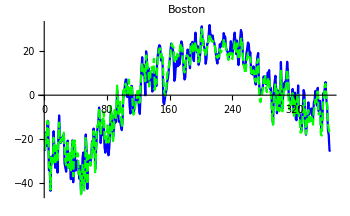
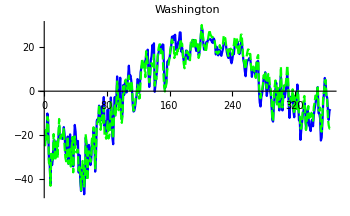
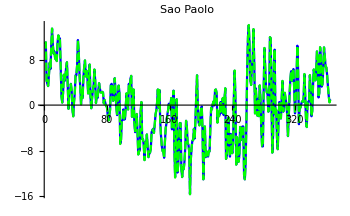
-Graphics- | 0.0135384
-Graphics- | 0.0148274
-Graphics- | 0.0000131709

```mathematica
(* Many apologies for the cluttered appearance of this code. I promise it isn't that bad. *)
cities={"Boston","Washington","Sao Paolo"};
Grid[Table[{ListLinePlot[{T[[i]],reconstructed[[i]]},PlotStyle->{Blue,Green},PlotMarkers->None,PlotLabel->cities[[i]],ImageSize->350],CorrelationDistance[T[[i]],reconstructed[[i]]]},{i,3}],Spacings->{0,3},Frame->{False,All}]
```

## Misc

Mathematica refuses to  simplify the fibonacci sequence when it gets large enough. This is very concerning.

```mathematica
FullSimplify[Q.MatrixPower[Λ,499].Inverse@Q.U0,TimeConstraint->Infinity]//MatrixForm
```

(-(1-√5)^500/(3273390607896141870013189696827599152216642046043064789483291368096133796404674554883270092325904157150886684127560071009217256545885393053328527589376 √5)+((1-√5)^500 (1+√5))/(6546781215792283740026379393655198304433284092086129578966582736192267592809349109766540184651808314301773368255120142018434513091770786106657055178752 √5)+(1+√5)^500/(3273390607896141870013189696827599152216642046043064789483291368096133796404674554883270092325904157150886684127560071009217256545885393053328527589376 √5)+((-1+√5) (1+√5)^500)/(6546781215792283740026379393655198304433284092086129578966582736192267592809349109766540184651808314301773368255120142018434513091770786106657055178752 √5)
-(1-√5)^499/(1636695303948070935006594848413799576108321023021532394741645684048066898202337277441635046162952078575443342063780035504608628272942696526664263794688 √5)+((1-√5)^499 (1+√5))/(3273390607896141870013189696827599152216642046043064789483291368096133796404674554883270092325904157150886684127560071009217256545885393053328527589376 √5)+(1+√5)^499/(1636695303948070935006594848413799576108321023021532394741645684048066898202337277441635046162952078575443342063780035504608628272942696526664263794688 √5)+((-1+√5) (1+√5)^499)/(3273390607896141870013189696827599152216642046043064789483291368096133796404674554883270092325904157150886684127560071009217256545885393053328527589376 √5))

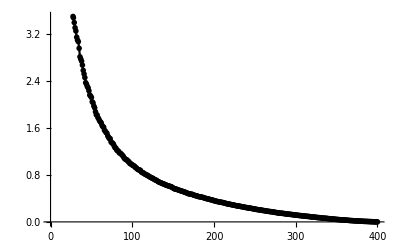

```mathematica
ListLinePlot[SingularValueList[ImageData@mark]]
```